## First define the genrator base

```mathematica
allGeneratorVariables=Sort[Table[
With[
{sets=ConnectedComponents[ GraphComplement[allGraphs4[k,"graph"]]]},
allGraphs4[k,"colofourgenerator"]=PartitionToSymbol[sets,"g"]
],
{k,allGraphs4GeneratorAtomKeys}
],CompareSymbols];
```

```mathematica
repFullToGen=ToRules[
Reduce[
Table[
allGraphs4[k,"colofourgenerator"]==allGraphs4[k,"colofour"]
,
{k,allGraphs4GeneratorAtomKeys}
],
Table[allGraphs4[k,"colofour"],{k,allGraphs4AtomKeys}]
]
];
```

```mathematica
Monitor[
Table[
allGraphs4[k,"colofourgenerator"]=Simplify[allGraphs4[k,"colofour"]/.repFullToGen],
{k,Sort[Keys[allGraphs4]]}
],k];
```

## Now define the base basic data

```mathematica
Bases4=Association[];
```

```mathematica
Bases4["C"]=Association[];
```

```mathematica
Bases4["C","Colofour"]="colofour";
```

```mathematica
Bases4["E"]=Association[];
```

```mathematica
Bases4["E","Colofour"]="colofourrealnull";
```

```mathematica
Bases4["G"]=Association[];
```

```mathematica
Bases4["G","Colofour"]="colofourgenerator";
```

```mathematica
allBases4={"C","E","G"}
```

{C,E,G}

## Compute keys and variables

```mathematica
Table[Bases4[base,"AtomKeys"]=Sort[Select[Keys[allGraphs4],Length[ListofVars[allGraphs4[#,Bases4[base,"Colofour"]]]]==1&],CompareSymbols[allGraphs4[#1,Bases4[base,"Colofour"]],allGraphs4[#2,Bases4[base,"Colofour"]]]&]
,{base,allBases4}];
```

```mathematica
Table[Bases4[base,"Variables"]=Table[allGraphs4[k,Bases4[base,"Colofour"]],{k,Bases4[base,"AtomKeys"]}]
,{base,allBases4}];
```

```mathematica
BaseCoeff4[key_,base_]:=Table[Coefficient[allGraphs4[key,Bases4[base,"Colofour"]],var],{var,Bases4[base,"Variables"]}]
```

```mathematica
BaseCoeff4[0,"E"]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ConversionMatrix4[base1_,base2_]:=Table[BaseCoeff4[key1,base2],{key1,Bases4[base1,"AtomKeys"]}]
```

```mathematica
Table[Bases4[base,"AtomKeys"],{base,allBases4}]//Flatten//DeleteDuplicates//Length
```

42

## Checking some conversion matrix identities

```mathematica
ConversionMatrix4["E","C"]==Transpose[ConversionMatrix4["G","C"]]
```

True

```mathematica
ConversionMatrix4["E","C"]==Inverse[ConversionMatrix4["C","E"]]
```

True

```mathematica
ConversionMatrix4["G","C"]==Transpose[Inverse[ConversionMatrix4["C","E"]]]
```

True

```mathematica
Table[base->ConversionMatrix4[base,base]==IdentityMatrix[42],{base,allBases4}]
```

{C→False,E→False,G→False}

## Viewing come COnversion matrcxes

```mathematica
Table[Det[ConversionMatrix4[base1,base2]],{base1,allBases4},{base2,allBases4}]
```

{{1,1,1},{1,1,1},{1,1,1}}

```mathematica
Table[base1->Eigenvalues[ConversionMatrix4[base1,base2]]//N,{base1,allBases4},{base2,{"G"}}]
```

{{C→{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}},{E→{0.+2.80588 ⅈ,0.-2.80588 ⅈ,0.+1. ⅈ,0.+1. ⅈ,0.+1. ⅈ,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ,0.-1. ⅈ,0.-1. ⅈ,0.-1. ⅈ,1.,0.+0.356394 ⅈ,0.-0.356394 ⅈ}},{G→{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}}

```mathematica
Table[base1->Det[ConversionMatrix4[base1,base2]],{base1,allBases4},{base2,{"G"}}]
```

{{C→1},{E→1},{G→1}}

```mathematica
Tally[Table[Sort[Map[Length,allGraphs4[k,"vertexsets"]]],{k,allGraphs4AtomKeys}]]
```

{{{1,1,1,1},1},{{1,1,2},6},{{1,3},4},{{2,2},3},{{4},1}}

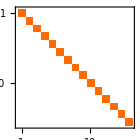
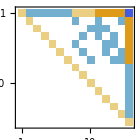
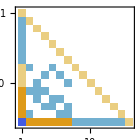
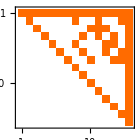
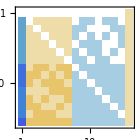
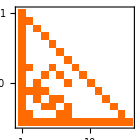
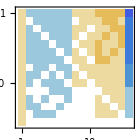
| C | E | G
C | -Graphics- | -Graphics- | -Graphics-
E | -Graphics- | -Graphics- | -Graphics-
G | -Graphics- | -Graphics- | -Graphics-

```mathematica
TableForm[Table[MatrixPlot[ConversionMatrix4[base1,base2],ImageSize->140],{base1,allBases4},{base2,allBases4}],TableHeadings->{allBases4, allBases4},TableAlignments->{Center, Center}]
```

```mathematica
TableForm[Table[MatrixPlot[Inverse[ConversionMatrix4[base1,base2]],ImageSize->140],{base1,allBases4},{base2,allBases4}],TableHeadings->{Reverse[allBases4], Reverse[allBases4]},TableAlignments->{Center, Center}]
```

| G | E | C
G | -Graphics- | -Graphics- | -Graphics-
E | -Graphics- | -Graphics- | -Graphics-
C | -Graphics- | -Graphics- | -Graphics-

```mathematica
ConversionMatrix4["G","E"].ConversionMatrix4["E","C"]==ConversionMatrix4["G","C"]
```

True

```mathematica
labels=Table [With[
{k=Bases4["E","AtomKeys"][[i]]},i->ShowGraph[allGraphs4,k]],{i,15}]
```

{1→-Graphics-0,2→-Graphics-2,3→-Graphics-18,4→-Graphics-6,5→-Graphics-486,6→-Graphics-162,7→-Graphics-54,8→-Graphics-488,9→-Graphics-168,10→-Graphics-72,11→-Graphics-26,12→-Graphics-666,13→-Graphics-546,14→-Graphics-218,15→-Graphics-728}

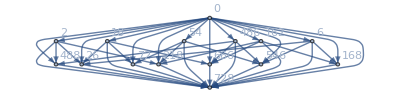
-Graphics-{15,45}

```mathematica
With[{g=AdjacencyGraph[ConversionMatrix4["E","C"]-IdentityMatrix[15],GraphLayout->"LayeredDigraphEmbedding",VertexLabels->labels]}
,Labeled[g,{VertexCount[g],EdgeCount[g]}]]
```

```mathematica
Keys[Bases4]
```

{C,E,G}

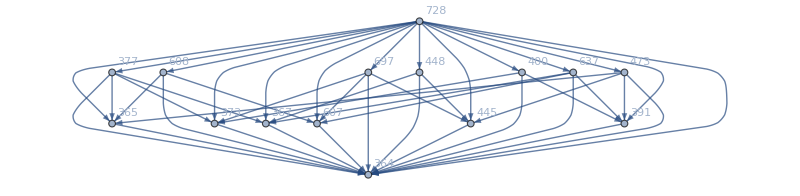
-Graphics-{15,45}

```mathematica
With[
{base1="G",base2="C"},
With[
{labels=Table [With[
{k=Bases4[base2,"AtomKeys"][[i]]},i->ShowGraph[allGraphs4,k]],{i,15}]},
With[{g=AdjacencyGraph[ConversionMatrix4[base1,base2]-IdentityMatrix[15],GraphLayout->"LayeredDigraphEmbedding",VertexLabels->labels,ImageSize->800]}
,Labeled[g,{VertexCount[g],EdgeCount[g]}]]
]
]
```

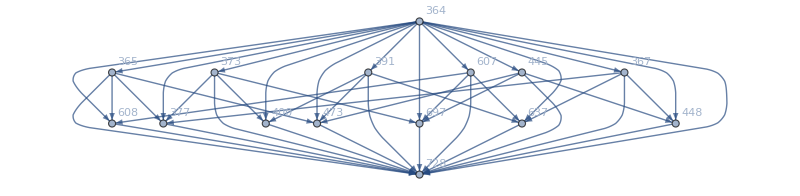
-Graphics-{15,45}

```mathematica
With[
{base1="E",base2="C"},
With[
{labels=Table [With[
{k=Bases4[base2,"AtomKeys"][[i]]},i->ShowGraph[allGraphs4,k]],{i,15}]},
With[{g=AdjacencyGraph[ConversionMatrix4[base1,base2]-IdentityMatrix[15],GraphLayout->"LayeredDigraphEmbedding",VertexLabels->labels,ImageSize->800]}
,Labeled[g,{VertexCount[g],EdgeCount[g]}]]
]
]
```

```mathematica
Total[CoefficientList[CharacteristicPolynomial[ConversionMatrix4["E","C"],x],x]]
```

0

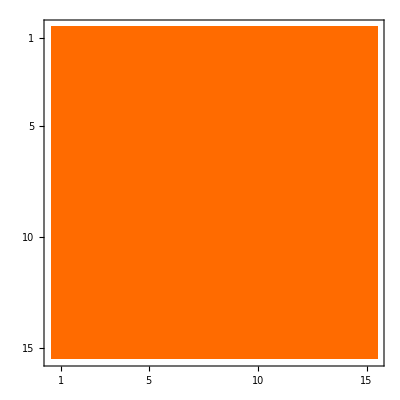

```mathematica
MatrixPlot[ConversionMatrix4["E","C"]+(CharacteristicPolynomial[ConversionMatrix4["E","C"],x]/.x->ConversionMatrix4["E","C"])]
```

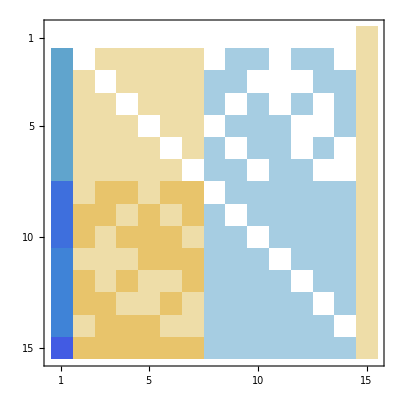

```mathematica
MatrixPlot[ConversionMatrix4["E","G"]]
```

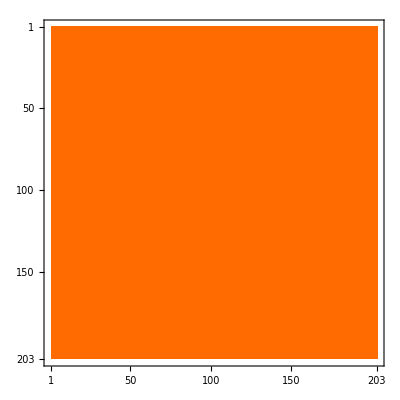

```mathematica
With[
{m=ConversionMatrix6["E","C"]},
MatrixPlot[m+(CharacteristicPolynomial[m,x]/.x->m)]
]
```

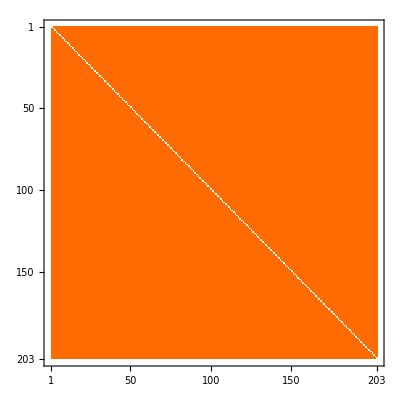

```mathematica
With[
{m=ConversionMatrix6["E","C"]},
MatrixPlot[(CharacteristicPolynomial[m,x]/.Power->MatrixPower/.x->m)]
]
```

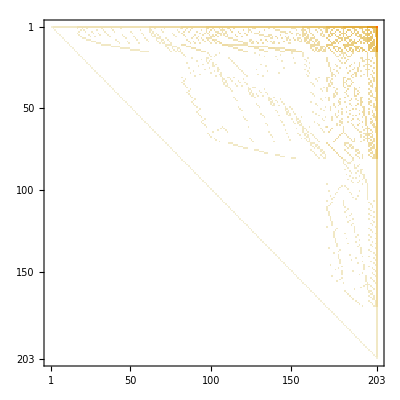

```mathematica
With[
{m=ConversionMatrix6["E","C"]},
MatrixPlot[(x.x/.x->m)]
]
```

```mathematica
x^2/.Power->MatrixPower
```

MatrixPower[x,2]

```mathematica
x^2
```

x^2

```mathematica
With[
{m=ConversionMatrix6["E","C"]},
MatrixPlot[(CharacteristicPolynomial[m,x]/.Power->MatrixPower/.x->m)]
]
```

-Graphics-

```mathematica
Plot[Table[PDF[WignerSemicircleDistribution[r],x],{r,{0.7,1.2,2}}]//Evaluate,{x,-2,2},Exclusions->None,Filling->Axis]
```

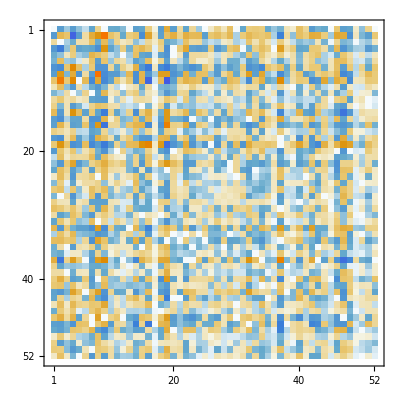

```mathematica
With[
{m=RandomVariate[GaussianOrthogonalMatrixDistribution[52]]},
MatrixPlot[(CharacteristicPolynomial[m,x]/.Power->MatrixPower/.x->m)]
]
```